## 模式+随机

## 模式+随机

无理数热图

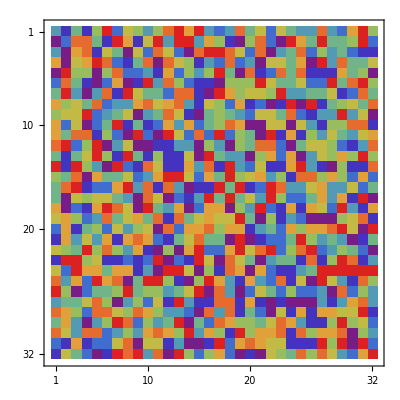
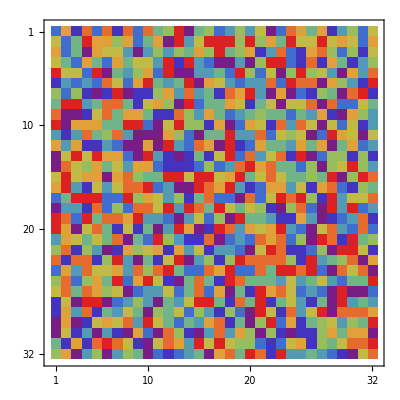
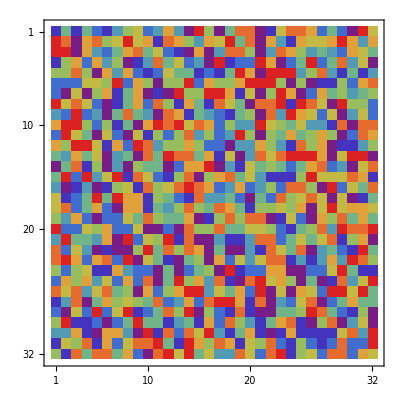
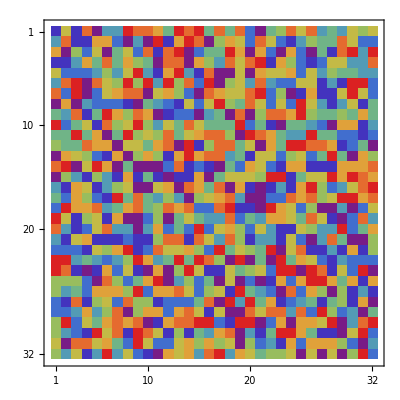

```mathematica
MatrixPlot[N[#,1024]//RealDigits//First//Partition[#,32]&,ColorFunctionScaling->False,ColorFunction->(ColorData["Rainbow"][Rescale[#,{0,9}]]&)]&/@{Pi,E,Sqrt@2,GoldenRatio}
```

随机游走

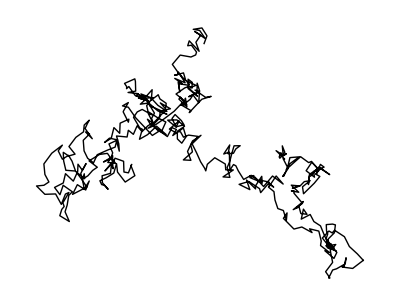

```mathematica
Graphics[Line[{Re[#],Im[#]}&/@Accumulate[RandomComplex[{-1-I,1+I},500]]]]
```

```mathematica
Graphics3D[Line[Accumulate[RandomChoice[{-1,1},{1000,3}]]]]
```

## Dirichlet 分布

### 狄利克雷分布

```mathematica
ContourPlot[PDF[DirichletDistribution[#],{x,y}],{x,0,1},{y,0,1},RegionFunction->Function[{x,y},x+y<1],PlotRange->All,ColorFunction->"TemperatureMap"]&/@{{1,2,4},{4,1,2},{2,4,1},{2,4,8},{4,8,2},{8,2,4}}
```

### 重心坐标系

```mathematica
TernaryListPlot[RandomReal[1,{4,5,3}],PlotMarkers->Automatic]
```

-Graphics-

```mathematica
TernaryListPlot[RandomReal[1,{15,3}]->Range[15]]
```

-Graphics-

重心坐标系中混合红绿蓝

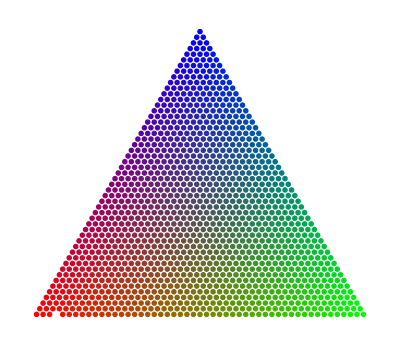

```mathematica
(*将三元坐标转换为笛卡尔坐标*)
ToCartesian[{x_,y_,z_}]:={y+z/2,(Sqrt[3]/2) z};

(*生成满足 i+j+k=1 的数据*)
data=Flatten[Table[{i,j,1-i-j},{i,0,1,0.02},{j,0,1-i,0.02}],1];

(*为每个数据点生成对应的 RGBColor*)
colors=RGBColor@@@data;

(*将数据点转换为笛卡尔坐标*)
coords=ToCartesian/@data;

(*使用 Graphics 绘制*)
Graphics[{PointSize[0.01],Transpose[{colors,Point/@coords}]},(*设置颜色和点*)AspectRatio->Sqrt[3]/2,(*设置比例*)Axes->False,(*显示坐标轴*)GridLines->Automatic,(*显示网格线*)GridLinesStyle->Directive[Gray,Dashed]]
```

在重心坐标系中绘制狄利克雷分布

```mathematica
(*Define the function to generate and plot the contour plot*)
DirichletTernaryContourPlot[alpha_List]:=Module[{data,pdfValues,cartesianData,contourData},(*Generate data points {x,y,z} with z=1-x-y*)data=Flatten[Table[{x,y,1-x-y},{x,0,1,0.01},{y,0,1-x,0.01}],1];
(*Compute PDF values using DirichletDistribution with {x,y}*)
pdfValues=PDF[DirichletDistribution[alpha],Most/@data];
(*Transform data to Cartesian coordinates*)
cartesianData=ToCartesian/@data;
(*Prepare data for contour plotting*)
contourData=Transpose[{cartesianData[[All,1]],cartesianData[[All,2]],pdfValues}];
(*Create the contour plot without labels*)
ListContourPlot[contourData,ColorFunction->"TemperatureMap",Contours->10,AspectRatio->Sqrt[3]/2,Frame->False,Axes->False,PlotRange->All]]
```

```mathematica
DirichletTernaryContourPlot/@{{2,1,1},{1,2,1},{1,1,2},{1,2,2},{2,1,2},{2,2,1},{4,2,1},{2,1,4},{2,4,1},{1,2,4},{1,4,2},{4,1,2}}
```

```mathematica
DirichletTernaryContourPlot/@{{4,2,2},{2,4,2},{2,2,4},{1,1,1},{2,2,2},{4,4,4},{4,2,8},{2,8,4},{2,4,8},{8,4,2},{4,8,2},{8,2,4}}
```

## 贝塞尔曲线

交互式贝塞尔曲线

```mathematica
Manipulate[Graphics[{BezierCurve[pts,SplineDegree->d],Dashed,Green,Line[pts]},PlotRange->5,Frame->True],{{pts,{{-3,0},{-1,3},{1,-3},{3,0}}},Locator,LocatorAutoCreate->True},{{d,3,"degree"},2,6,1}]
```

三维空间中的贝塞尔曲线

```mathematica
pts={{0,0,0},{1,1,1},{2,-1,1},{3,0,2}};Graphics3D[{BezierCurve[pts],Green,Line[pts],Red,Point[pts]}]
```

字轮廓的资源函数

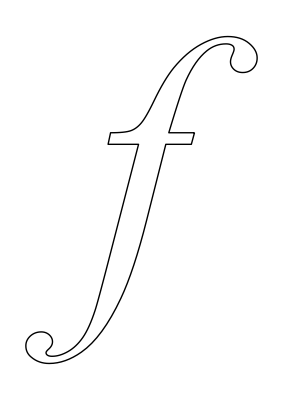

```mathematica
ResourceFunction["CharacterCurves"][Style["f",Italic,FontFamily->"Times New Roman"]]
```

## 繁花曲线

### 内旋轮线

```mathematica
HypotrochoidPlot[R_,r_,d_]:=ParametricPlot[{(R-r) Cos[θ]+d Cos[((R-r)/r) θ],(R-r) Sin[θ]-d Sin[((R-r)/r) θ]},{θ,0,2 Pi Denominator[Rationalize[R/r,10^-10]]},PlotRange->All,ColorFunction->(Hue[#3/(2 Pi)]&),ColorFunctionScaling->False]
```

```mathematica
Table[HypotrochoidPlot[R,1,d],{R,{2,3,4,5,6}},{d,{0,.5,1,2}}]
```

```mathematica
HypotrochoidPlot@@@{{23,9,13},{23,9,19},{57,29,9},{57,29,19},{59,19,19},{59,29,29}}
```

### 外旋轮线

```mathematica
EpitrochoidPlot[R_,r_,d_]:=ParametricPlot[{(R+r) Cos[θ]-d Cos[((R+r)/r) θ],(R+r) Sin[θ]-d Sin[((R+r)/r) θ]},{θ,0,2 Pi Denominator[Rationalize[R/r,10^-10]]},PlotRange->All,ColorFunction->(Hue[#3/(2 Pi)]&),ColorFunctionScaling->False]
```

```mathematica
Table[EpitrochoidPlot[R,1,d],{R,1,5},{d,{0,.5,1,2}}]
```

```mathematica
EpitrochoidPlot@@@{{23,9,13},{23,9,19},{57,29,9},{57,29,19},{59,19,19},{59,29,29}}
```

## 分形

### 科赫雪花

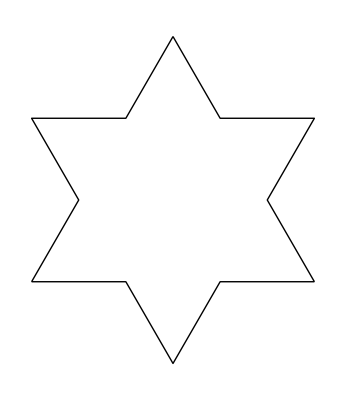
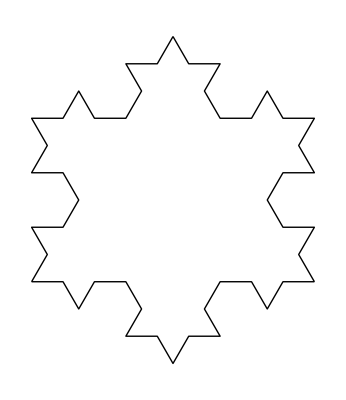
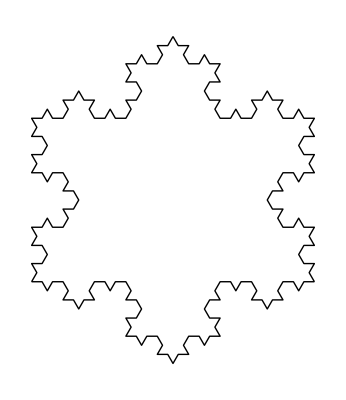
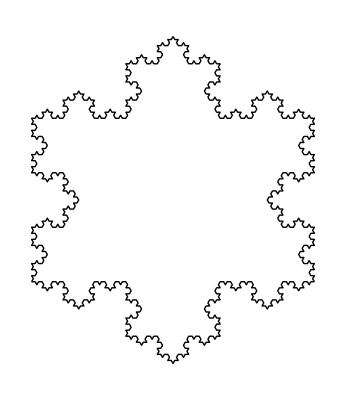

```mathematica
Table[Graphics[GeometricTransformation[KochCurve[i],{RotationTransform[Pi,{1/2,0}],RotationTransform[-Pi/3,{1,0}],RotationTransform[Pi/3,{0,0}]}]],{i,4}]
```

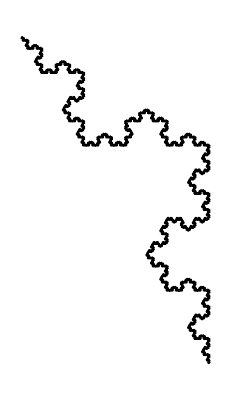

```mathematica
Graphics[Line[AnglePath[Array[ThueMorse,4096] 2 Pi/3]]]
```

### 谢尔宾斯基三角形

```mathematica
Row[{Table[SierpinskiMesh[n],{n,0,5}]},Spacer[40]]
```

```mathematica
Row[{Table[SierpinskiMesh[n,3],{n,0,5}]},Spacer[40]]
```

### 谢尔宾斯基地毯

```mathematica
Row[{Table[MengerMesh[n],{n,0,5}]},Spacer[40]]
```

```mathematica
Row[{Table[MengerMesh[n,3],{n,0,3}]},Spacer[40]]
```

### 龙曲线

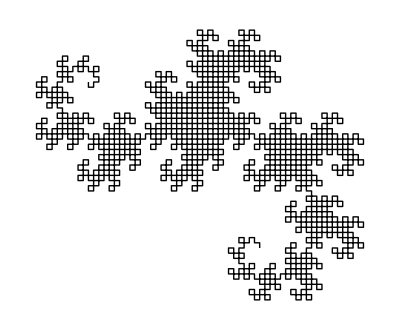

```mathematica
Graphics[Line[AnglePath[{90 °,-90 °}[[1+Nest[Join[#,{0},Reverse[1-#]]&,{0},10]]]]]]
```

### 巴恩斯利蕨

```mathematica
BarnsleyFern[n_Integer]:=Module[{transforms,nextPoint,pts},transforms={{{{0.85,0.04},{-0.04,0.85}},{0,1.6},0.85},{{{-0.15,0.28},{0.26,0.24}},{0,0.44},0.07},{{{0.2,-0.26},{0.23,0.22}},{0,1.6},0.07},{{{0,0},{0,0.16}},{0,0},0.01}};
nextPoint[pt_]:=Module[{r=RandomReal[]},Which[r<0.85,transforms[[1,1]].pt+transforms[[1,2]],r<0.92,transforms[[2,1]].pt+transforms[[2,2]],r<0.99,transforms[[3,1]].pt+transforms[[3,2]],True,transforms[[4,1]].pt+transforms[[4,2]]]];
pts=NestList[nextPoint,{0.0,0.0},n];
ListPlot[pts,AspectRatio->Automatic,PlotStyle->{Green,PointSize[Tiny]},PlotRange->All]]
```

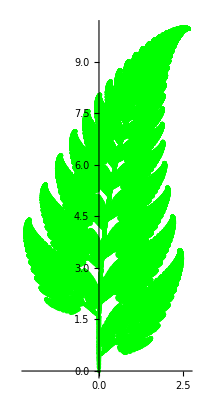

```mathematica
BarnsleyFern[100000]
```

### 曼德博集合

```mathematica
MandelbrotSetPlot[]
```

-Graphics-

### 朱利亚集合

```mathematica
cs=RandomComplex[{-1-1 I,1+1 I},6];
```

```mathematica
Table[Labeled[JuliaSetPlot[cs[[i]]],"c = "<>ToString[cs[[i]]]],{i,1,6}]
```

## 网络图

生成由字典中“相近”的词组成的一个网络

```mathematica
words=DictionaryLookup["wol*"];
```

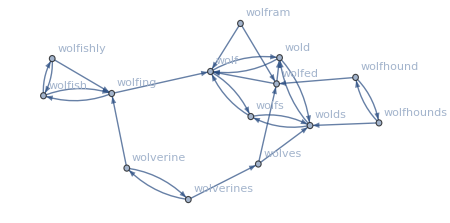

```mathematica
Flatten[Map[(Thread[#->DeleteCases[Nearest[words,#,3],#]])&,words]];
Graph[%,VertexLabels->"Name",ImageSize->450]
```

```mathematica
Flatten[Map[(Thread[#->DeleteCases[Nearest[words,#,3],#]])&,words]];
Graph3D[%,VertexLabels->"Name"]
```

-Graphics3D-

邻接矩阵绘图，对称矩阵为无向图

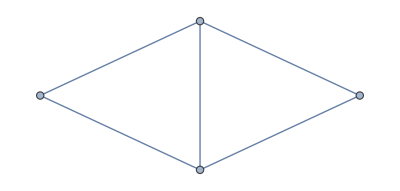

```mathematica
AdjacencyGraph[({{0,1,1,0},{1,0,1,1},{1,1,0,1},{0,1,1,0}})]
```

非对称矩阵为有向图

```mathematica
AdjacencyGraph[({{0,1,0,0},{1,0,0,0},{1,1,0,0},{1,1,0,0}})]
```

-Graphics-